# Channel Final Values

```mathematica
Needs["VectorAnalysis`"]
SetCoordinates[Cartesian[x,y,z]]
CoordinateSystem
CoordinateRanges[]
```

Cartesian[x,y,z]

Cartesian

{-∞<x<∞,-∞<y<∞,-∞<z<∞}

```mathematica
Laplacian[qwew[y]qwqeasd[z]]
```

qwqeasd[z] qwew''[y]+qwew[y] qwqeasd''[z]

```mathematica
ClearAll[u1,v1,w1,um,u2,v2,w2,u31,v31,w31,u33,v33,w33]
```

## O(δ) Plots

```mathematica
V1[y_,k_]:=k y Exp[-k y]
U1[y_,k_]:=-(((k^2)(y^2)+k y) /(4(k^2)))Exp[-k y]
W1[y_,k_]:=(k y-1)Exp[-k y]
```

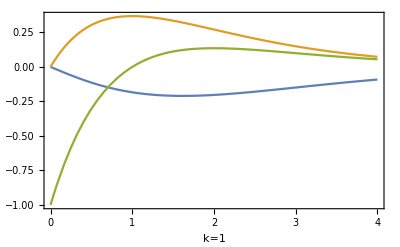
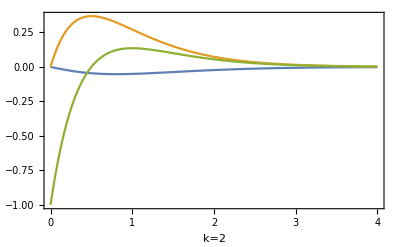
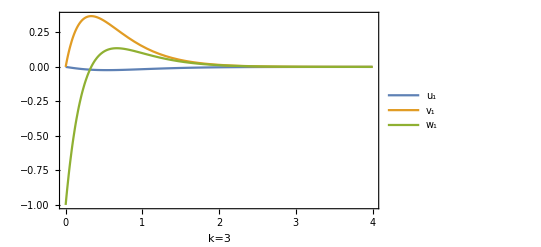

```mathematica
Flatten[Table[{{Plot[{U1[y,1],V1[y,1],W1[y,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=1"]},{Plot[{U1[y,2],V1[y,2],W1[y,2]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=2"]},{Plot[{U1[y,3],V1[y,3],W1[y,3]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=3",PlotLegends->{"u_1","v_1","w_1"}]}},1]]
```

```mathematica
Manipulate[Plot[{U1[y,k],V1[y,k],W1[y,k]},{y ,0,6},Frame->True,PlotRange->All,PlotLegends->{"u_1","v_1","w_1"}],{k,1,5,1,Appearance->"Labeled"},FrameLabel->{"y"}];
```

## O(δ^2) Plots

```mathematica
UM[y_,k_]:=(-5+ⅇ^(-2 k y) (5+2 k y (5+k y (5+2 k y))))/(64 k^3)
V2[y_,k_,a_]:=(ⅇ^(-2 k y) (3+8 k (-3/(8 k)+y+k y^2+16 y F2[a,k] )))/(128 k)
W2[y_,k_,a_]:=(ⅇ^(-2 k y) (-1+2 k^2 y^2+16 F2 [a,k](-1+2 k y)))/(32 k)
U2[y_,k_,a_]:=(ⅇ^(-2 k y) y (-3-96 F2[a,k] (1+2 k y)+2 k y (-3+4 k y)))/(1536 k^2)
```

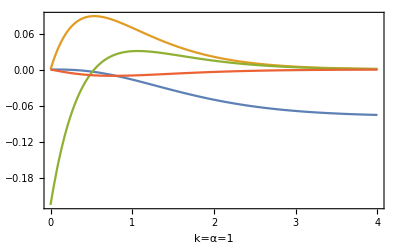
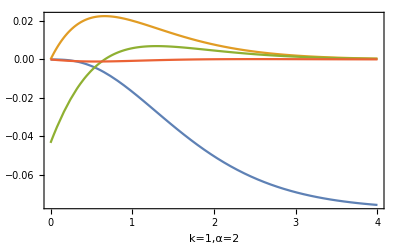
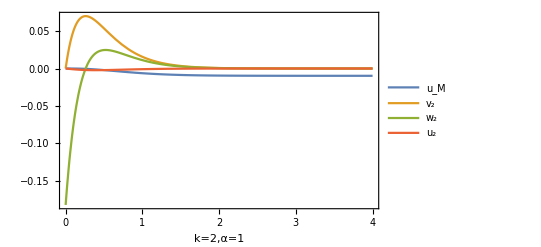

```mathematica
Flatten[Table[{{Plot[{UM[y,1],V2[y,1,1],W2[y,1,1],U2[y,1,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=α=1"]},{Plot[{UM[y,1],V2[y,1,2],W2[y,1,2],U2[y,1,2]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=1,α=2"]},{Plot[{UM[y,2],V2[y,2,1],W2[y,2,1],U2[y,2,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=2,α=1",PlotLegends->{"u_M","v_2","w_2","u_2"}]}},1]]
```

```mathematica
F2[a_,k_]:=(-11 a^4-8 a^2 k^2+243 k^4)/(288 k^2 (a^2+k^2))
```

## O(d^3A’)

```mathematica
ClearAll[V33,U33,W33]
```

```mathematica
F3:=0
```

```mathematica
V33[y_,k_]:=(ⅇ^(-k y) (-3-4 k y+k^2 (3/k^2-2 y^2+8 y F3)))/(8 k^2)
W33[y_,k_]:=-(ⅇ^(-k y) (-2+4 F3 k-4 F3 k^2 y+k^2 y^2))/(4 k^2)
U33[y_,k_]:=1/(96 k^4)ⅇ^(-k y) (15+3 (-5+4 F3 k)-12 F3 k (1+2 k y (1+k y))+2 k y (15+k y (15+4 k y)))
```

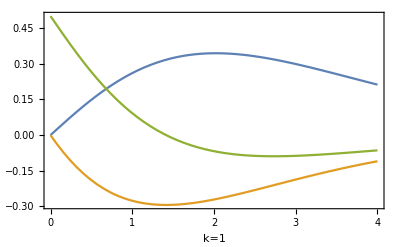
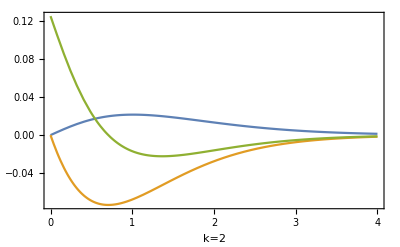
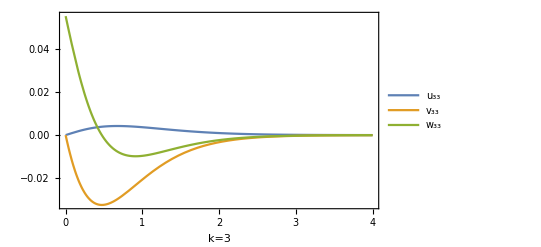

```mathematica
Flatten[Table[{{Plot[{U33[y,1],V33[y,1],W33[y,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=1"]},{Plot[{U33[y,2],V33[y,2],W33[y,2]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=2"]},{Plot[{U33[y,3],V33[y,3],W33[y,3]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=3",PlotLegends->{"u_33","v_33","w_33"}]}},1]]
```

## O(d^3A^3)

```mathematica
ClearAll[U31,V31,W31]
```

```mathematica
V31[y_,k_,a_]:=1/(4096 k^2)ⅇ^(-3 k y) (37+32 F2[a,k] (3+4 k y)+4 k y (13+6 k y)+ⅇ^(2 k y) (-37-96 F2[a,k]+4096 k^2 y F3))
W31[y_,k_,a_]:=1/(4096 k^2)ⅇ^(-3 k y) (59+160 F2[a,k]+12 k y (9+32 F2[a,k]+6 k y)+ⅇ^(2 k y) (-37-96 F2[a,k]+4096 F3  k (-1+k y)))
U31[y_,k_,a_]:=1/(98304 k^4)ⅇ^(-3 k y) (-6039-3 ⅇ^(2 k y) (-2013-384 F2[a,k] (-4+k y)+4 k y (-37+2048 F3  k (1+k y)))+384 F2[a,k] (12+k y (25+2 k y (15+8 k y)))-8 k y (1467+2 k y (663+2 k y (175+46 k y))))
```

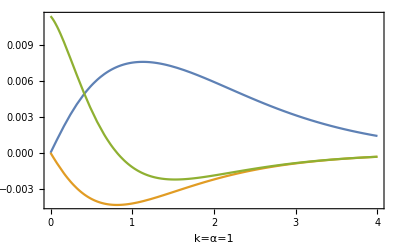
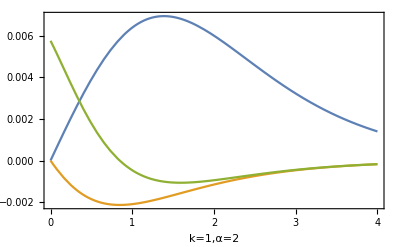
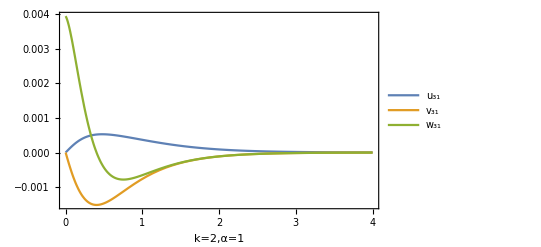

```mathematica
Flatten[Table[{{Plot[{U31[y,1,1],V31[y,1,1],W31[y,1,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=α=1"]},{Plot[{U31[y,1,2],V31[y,1,2],W31[y,1,2]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=1,α=2"]},{Plot[{U31[y,2,1],V31[y,2,1],W31[y,2,1]},{y,0,4},Frame->True,PlotRange->All,AxesLabel->{y},FrameLabel->"k=2,α=1",PlotLegends->{"u_31","v_31","w_31"}]}},1]]
```

## All Velocity Field Terms

```mathematica
v1[y_]:=k ⅇ^(-k y) y 
w1[y_]:=ⅇ^(-k y) (-1+k y)
u1[y_]:=-(ⅇ^(-k y)  y (1+k y))/(4 k)
um[y_]:=(-5+ⅇ^(-2 k y) (5+2 k y (5+k y (5+2 k y))))/(64 k^3)
v2[y_]:=(ⅇ^(-2 k y) (3+8 k (-3/(8 k)+y+k y^2+16 y F2 )))/(128 k)
w2[y_]:=(ⅇ^(-2 k y) (-1+2 k^2 y^2+16 F2 (-1+2 k y)))/(32 k)
u2[y_]:=1/(1536 k^2)ⅇ^(-2 k y) y (-3-96 F2 (1+2 k y)+2 k y (-3+4 k y))
v33[y_]:=(ⅇ^(-k y) (-3-4 k y+k^2 (3/k^2-2 y^2+8 y F3)))/(8 k^2)
w33[y_]:=-(ⅇ^(-k y) (-2+4 F3 k-4 F3 k^2 y+k^2 y^2))/(4 k^2)
u33[y_]:=1/(96 k^4)ⅇ^(-k y) (15+3 (-5+4 F3 k)-12 F3 k (1+2 k y (1+k y))+2 k y (15+k y (15+4 k y)))
v31[y_]:=1/(4096 k^2)ⅇ^(-3 k y) (37+32 F2 (3+4 k y)+4 k y (13+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 k^2 y F3))
w31[y_]:=1/(4096 k^2)ⅇ^(-3 k y) (59+160 F2+12 k y (9+32 F2+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 F3  k (-1+k y)))
u31[y_]:=1/(98304 k^4)ⅇ^(-3 k y) (-6039-3 ⅇ^(2 k y) (-2013-384 F2 (-4+k y)+4 k y (-37+2048 F3  k (1+k y)))+384 F2 (12+k y (25+2 k y (15+8 k y)))-8 k y (1467+2 k y (663+2 k y (175+46 k y))))
```

```mathematica
FullSimplify[w31[y]]
```

1/(4096 k^2)ⅇ^(-3 k y) (59+160 F2+12 k y (9+32 F2+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 F3 k (-1+k y)))

```mathematica
FullSimplify[u31[y]]
```

1/(98304 k^4)ⅇ^(-3 k y) (-6039-3 ⅇ^(2 k y) (-2013-384 F2 (-4+k y)+4 k y (-37+2048 F3 k (1+k y)))+384 F2 (12+k y (25+2 k y (15+8 k y)))-8 k y (1467+2 k y (663+2 k y (175+46 k y))))

```mathematica
FullSimplify[v31[y]]
```

1/(4096 k^2)ⅇ^(-3 k y) (37+32 F2 (3+4 k y)+4 k y (13+6 k y)+ⅇ^(2 k y) (-37-96 F2+4096 F3 k^2 y))

```mathematica
Apart[u31[y]]
```

-1/(32768 k^4)ⅇ^(-k y) (-2013+1536 F2-148 k y-384 F2 k y+8192 F3 k^2 y+8192 F3 k^3 y^2)-1/(98304 k^4)ⅇ^(-3 k y) (6039-4608 F2+11736 k y-9600 F2 k y+10608 k^2 y^2-11520 F2 k^2 y^2+5600 k^3 y^3-6144 F2 k^3 y^3+1472 k^4 y^4)

```mathematica
FullSimplify[u33[y]]
```

(ⅇ^(-k y) y (15-12 F3 k (1+k y)+k y (15+4 k y)))/(48 k^3)

```mathematica
FullSimplify[v33[y]]
```

-(ⅇ^(-k y) y (2-4 F3 k+k y))/(4 k)

```mathematica
FullSimplify[w33[y]]
```

(ⅇ^(-k y) (2-k^2 y^2+4 F3 k (-1+k y)))/(4 k^2)

## All λ Terms

```mathematica
ClearAll[lambda1,lambda2,lambdam,lambda31,lambda33]
```

```mathematica
lambda[z_]:=1+(delta) lambda1 Cos[k z]+(delta^2)lambda2 Cos[2 k z]+(delta^2) lambdam+(delta^3)lambda31 Cos[k z]+(delta^3) lambda32 Cos[3 k z]+(delta^3) lambda33 Cos[k z]
```

```mathematica
lambda1:=A[t]u1'[0]
lambda2:=((A[t])^2)u2'[0]
lambdam:=((A[t])^2) um'[0]
lambda31:=((A[t])^3)u31'[0]
lambda33:=(A'[t])u33'[0]
```

## All Q Terms

```mathematica
ClearAll[Q0,Q1,Qm,Q2,Q3]
```

```mathematica
Q0:=-1/a^2
Q1:=-(5 lambda1)/(3 (a^2+k^2))
```

```mathematica
Qm:=1/(36 a^2)(-36 Gmmhat-10 lambda1^2-60 lambdam-27 k^2 lambda1 Q1)
```

```mathematica
FullSimplify[Qm]
```

-1/(36 a^2)(36 Gmmhat+10 lambda1^2+60 lambdam+27 k^2 lambda1 Q1)

```mathematica
Q2:=(-10 lambda1^2-60 lambda2+27 k^2 lambda1 Q1)/(36 (a^2+4 k^2))
```

```mathematica
FullSimplify[Q2]
```

(-10 (lambda1^2+6 lambda2)+27 k^2 lambda1 Q1)/(36 (a^2+4 k^2))

```mathematica
Q3:=1/(216 (a^2+k^2))(-360 Gmmhat lambda1+10 lambda1^3-120 lambda1 lambda2-360 lambda31-360 lambda33-240 lambda1 lambdam+81 k^2 lambda1^2 Q1-324 k^2 lambda2 Q1-324 k^2 lambda1 Q2)
```

```mathematica
FullSimplify[Q3]
```

-((360 Gmmhat lambda1-10 lambda1^3+360 (lambda31+lambda33)-81 k^2 lambda1^2 Q1+324 k^2 lambda2 Q1+12 lambda1 (10 lambda2+20 lambdam+27 k^2 Q2))/(216 (a^2+k^2)))

#### Simplification of A Terms

```mathematica
FullSimplify[Q1]
```

(5 A[t])/(12 k (a^2+k^2))

```mathematica
Collect[Qm,A[t]]
```

-Gmmhat/a^2+((-5/(8 k^2)+45/(16 (a^2+k^2))) A[t]^2)/(36 a^2)

```mathematica
Collect[Q2,A[t],Simplify]
```

(5 (a^2 (-13+96 F2)+(-85+96 F2) k^2) A[t]^2)/(4608 k^2 (a^2+k^2) (a^2+4 k^2))

```mathematica
Collect[Q3,A[t],Simplify]
```

(5 Gmmhat A[t])/(12 k (a^2+k^2))-(5 (a^2 k^2 (5831+8448 F2-184320 F3 k)+a^4 (1267+3072 F2-36864 F3 k)-16 k^4 (-265+312 F2+9216 F3 k)) A[t]^3)/(442368 k^3 (a^2+k^2)^2 (a^2+4 k^2))+(5 (-5+4 F3 k) A'[t])/(48 k^3 (a^2+k^2))

## Final Condition

```mathematica
ClearAll[modofc,F2,coeff]
```

```mathematica
modofc:=(3 A[t] w1[0])/(2 k Q0 Q1)
```

```mathematica
Solve[18/5 a^2 (a^2+k^2)==9(Gmm0)(ai)(a^(10/3)),Gmm0]
```

{{Gmm0→(2 (a^2+k^2))/(5 a^(4/3) ai)}}

```mathematica
N[(AiryAi'[0])^2]
```

0.0669875

```mathematica
((Sinh[2k]^2-4k^2)/(Sinh[2k]^2-8k^3Coth[2k]))
```

```mathematica
(*((Sinh[2k]^2-4k^2)/(Sinh[2k]^2-8k^3Coth[2k]))*)
```

```mathematica
Gamma0[a_,k_]:=(2 (a^2+k^2))/(5 a^(4/3) (AiryAiPrime[0]^2))
```

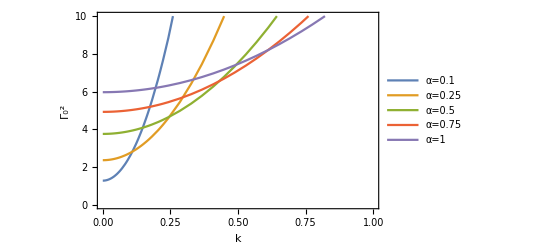

```mathematica
Plot[{Gamma0[a,k]/.a->0.1,Gamma0[a,k]/.a->0.25,Gamma0[a,k]/.a->0.5,Gamma0[a,k]/.a->0.75,Gamma0[a,k]/.a->1},{k,0,2},PlotLegends->{"α=0.1","α=0.25","α=0.5","α=0.75","α=1"},Frame->True,PlotRange->{{0,1},{0,10}},Axes->Automatic,FrameLabel->{"k","Γ_0^2"}]
```

```mathematica
Solve[(delta^2 (-a^2 k modofc Q1^2 Sin[2 k z]+k^3 modofc Q1^2 Sin[2 k z]-4 a^2 k modofc Q0 Q2 Sin[2 k z]))/a^2==-3 delta^2 (lambda1 A[t] Sin[2 k z] w1[0]+A[t]^2 Sin[2 k z] w2[0]),F2]
```

{{F2→(-11 a^4-8 a^2 k^2+243 k^4)/(288 k^2 (a^2+k^2))}}

```mathematica
F2:=(-11 a^4-8 a^2 k^2+243 k^4)/(288 k^2 (a^2+k^2))
```

```mathematica
FullSimplify[-3/4 delta^3 (lambda1^2 A[t] Sin[k z] w1[0]-4 lambda2 A[t] Sin[k z] w1[0]+8 lambdam A[t] Sin[k z] w1[0]+4 lambda1 A[t]^2 Sin[k z] w2[0]+4 A[t]^3 Sin[k z] w31[0]+4 Sin[k z] w33[0] A'[t])==+1/a^2 delta^3 (-a^2 k modofc Q1 Q2 Sin[k z]-2 k^3 modofc Q1 Q2 Sin[k z]-2 a^2 k modofc Q0 Q3 Sin[k z]-2 a^2 k modofc Q1 Qm Sin[k z])]
```

(delta Sin[k z] (221184 Gmmhat k^4 (a^2+k^2)^2 A[t]+(242 a^6-2401 a^4 k^2-11100 a^2 k^4+183 k^6) A[t]^3-82944 k^2 (a^2+k^2)^2 A'[t]))/(k (a^2+k^2))==0

```mathematica
Collect[Solve[1/(k (a^2+k^2))delta Sin[k z] (221184 Gmmhat k^4 (a^2+k^2)^2 A[t]+(242 a^6-2401 a^4 k^2-11100 a^2 k^4+183 k^6) A[t]^3-82944 k^2 (a^2+k^2)^2 A'[t])==0,A'[t]],A[t],Simplify]
```

{{A'[t]→8/3 Gmmhat k^2 A[t]+((242 a^6-2401 a^4 k^2-11100 a^2 k^4+183 k^6) A[t]^3)/(82944 k^2 (a^2+k^2)^2)}}

```mathematica
UndulationCoeff[a_,k_]:=(242 a^6-2401 a^4 k^2-11100 a^2 k^4+183 k^6)/(82944 k^2 (a^2+k^2)^2)
```

```mathematica
newnew[b_]:=(242 (b^6)-2401 b^4-11100 b^2+183)/(82944 ((b^2)+1)^2)
```

```mathematica
N[Solve[newnew[b]==0,b]]
```

{{b→0.-1.85671 ⅈ},{b→0.+1.85671 ⅈ},{b→-0.128173},{b→0.128173},{b→-3.6541},{b→3.6541}}

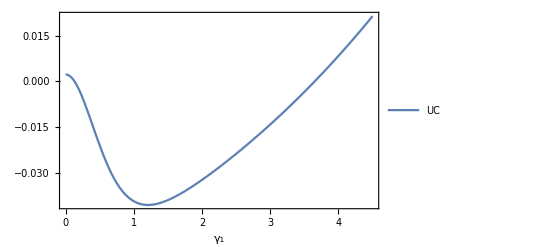

```mathematica
Plot[newnew[b],{b,0,4.5},PlotLegends->{"UC"},Axes->True,Frame->True,AxesLabel->{"γ_1"}]
```

```mathematica
Changed[b_]:=(242 (b^6)-2401 b^4-11100 b^2+183)/(82944 ((b^4)+2(b^2)+1))
```

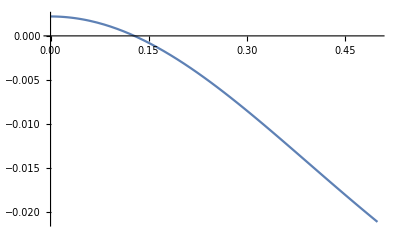

```mathematica
Plot[Changed[b],{b,0,0.5}]
```

```mathematica
Expand[(k^2)(a^2+k^2)^2(1/k^6)]
```

1+a^4/k^4+(2 a^2)/k^2

```mathematica
Plot3D[UndulationCoeff[a,k],{k,0.005,0.009},{a,0.005,0.009},ColorFunction->"Rainbow",PlotRange->All,Mesh->All,AxesLabel->{"α","k"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[UndulationCoeff[a,k],{k,0.005,0.05},{a,0.005,0.05},ColorFunction->"Rainbow",PlotRange->All,Mesh->All,AxesLabel->{"k","α"},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Plot[UndulationCoeff[a,k],{k,0.05,10},PlotRange->All,Frame->{{True,False}{True,False}}Axes->True,AxesLabel->{"k"},PlotLegends->"Coefficient"],{a,0.05,5,0.05,Appearance->"Labeled"}]
```

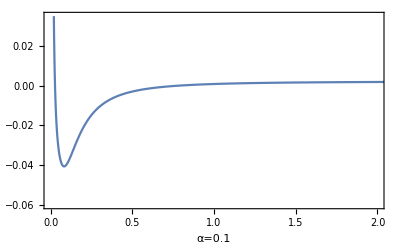

```mathematica
Plot[UndulationCoeff[0.1,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}},FrameLabel->{"α=0.1"}]
```

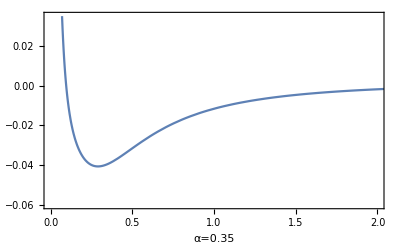

```mathematica
Plot[UndulationCoeff[0.35,k],{k,0,10},Frame->True,FrameLabel->{"α=0.35"},Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}}]
```

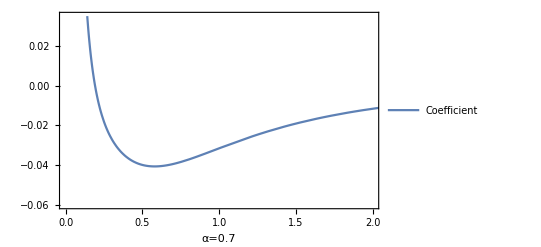

```mathematica
Plot[UndulationCoeff[0.7,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}},PlotLegends->{"Coefficient"},FrameLabel->{"α=0.7"}]
```

```mathematica
Flatten[Table[{{Plot[UndulationCoeff[0.1,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}},FrameLabel->{"α=0.1"}]},{Plot[UndulationCoeff[0.35,k],{k,0,10},Frame->True,FrameLabel->{"α=0.35"},Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}}]},{Plot[UndulationCoeff[0.7,k],{k,0,10},Frame->True,Axes->True,AxesLabel->{"k"},PlotRange->{{0,2},{-0.06,0.035}},PlotLegends->{"Coefficient"},FrameLabel->{"α=0.7"}]}},1]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
N[UndulationCoeff[3,1000]]
```

0.00220506